## Simple Demo file to LHAPDF Tables:

Demonstration to show how to use LHAPDF PDF tables with ManeParse
This is a simpler demo file that just shows the basics of loading the PDFs.

Please cite: 
ManeParse : A Mathematica reader for Parton Distribution Functions
D.B.Clark, E.Godat, F.I.Olness
Published in : Comput.Phys.Commun .216 (2017) 126 - 137
e - Print : 1605.08012[hep - ph]

BUG:  (April 2021: Version 4.0)
In the xxx.info file, input fields (such as “SetDesc:” ) CANNOT be split across multiple lines. 
While this is valid YAML, ManeParse reads a single line (record) at a time.
The “patch” for this is simply remove \newlines. 
E.g., 
	SetDesc: “This will BREAK \cr
		the ManeParse Program”
	SetDesc: “This will NOT break the ManeParse Program”

### Fred : 19 April 2021

```mathematica
Clear["Global`*"];
```

```mathematica
$Version
```

```mathematica
"12.1.0 for Linux x86 (64-bit) (March 14, 2020)"
```

12.1.0 for Linux x86 (64-bit) (March 14, 2020)

## Set Directory

#### This example notebook is written with relative directories and is intended to be run within the folder extracted from the tarball.

```mathematica
(* This just drops the leading path info to make the list of files easier to read *)
dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&;
```

```mathematica
NotebookDirectory[];
here=NotebookDirectory[]
```

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01/

```mathematica
(* If there is a problem with the Mathematica working directory, 
you can enter it manually here *)
SetDirectory[here]
```

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01

```mathematica
(* This shows what files should be in this main directory *)
FileNames["*",here] //dropPath
```

```mathematica
{"LHAPDF","MP_packages","testPDF_v01.nb"}
```

{LHAPDF,MP_packages,testPDF_v01.nb}

## Setup Other Directories

```mathematica
dirPackages=here<>"MP_packages";
FileNames["*",dirPackages] //dropPath
```

{pdfCalc.m,pdfErrors.m,pdfParseCTEQ.m,pdfParseLHA.m,README_V05.TXT,README_V05.TXT~}

```mathematica
dirFilesLHA="/usr/local/share/LHAPDF";
dirFilesLHA=here<>"/LHAPDF";
dirList=FileNames["*",dirFilesLHA];
dirList //dropPath
```

```mathematica
{"nCTEQ15FullNuc_1_1","nCTEQ15FullNuc_208_82"}
```

{nCTEQ15FullNuc_1_1,nCTEQ15FullNuc_208_82}

## Load the package

#### Loading the main package provides many useful functions

```mathematica
Get[dirPackages<>"/pdfParseLHA.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfParseCTEQ.m"]
```

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfErrors.m"]
```

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

#### All functions begin with ' pdf'. To obtain a list of available functions, type the command '?pdf*'.

```mathematica
?pdf*
```

## Individual file manipulation

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

#### Individual files in either LHA or PDS format can be parsed using the functions loaded from the packages. Here we demonstrate the LHA parsing function

```mathematica
?pdfParseLHA
```

```mathematica
fileList=dirList //First;
fileList //dropPath
```

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1

```mathematica
FileNames["*",dirList[[1]] ] //dropPath
```

{nCTEQ15FullNuc_1_1_0000.dat,nCTEQ15FullNuc_1_1.info}

```mathematica
{fileDat,fileInfo}=FileNames["*",dirList[[1]] ]
```

{/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1/nCTEQ15FullNuc_1_1_0000.dat,/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1/nCTEQ15FullNuc_1_1.info}

```mathematica
pdfParseLHA[fileInfo,fileDat]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1/nCTEQ15FullNuc_1_1.info.

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1/nCTEQ15FullNuc_1_1_0000.dat.

1

```mathematica
?pdfFamilyParseLHA
```

```mathematica
dirList[[2]]
```

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_208_82

```mathematica
(* CAUTION: For this demo file, only 3 error PDF tables are included to save space *)
pdfFamilyParseLHA[dirList[[2]] ]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01/LHAPDF/nCTEQ15FullNuc_208_82/nCTEQ15FullNuc_208_82.info.

Included 3 files in the PDF family.

{2,3,4}

```mathematica
pdfSetListDisplay[]
```

Set Number | File Name | Max Flavors | Valance Flavors
1 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01//LHAPDF/nCTEQ15FullNuc_1_1/nCTEQ15FullNuc_1_1_0000.dat | 5 | n/a
2 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01/LHAPDF/nCTEQ15FullNuc_208_82/nCTEQ15FullNuc_208_82_0000.dat | 5 | n/a
3 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01/LHAPDF/nCTEQ15FullNuc_208_82/nCTEQ15FullNuc_208_82_0001.dat | 5 | n/a
4 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/PDF_DEMO_v01/LHAPDF/nCTEQ15FullNuc_208_82/nCTEQ15FullNuc_208_82_0002.dat | 5 | n/a

## Test PDFs

#### The function “pdf” is left to be defined by the user. Access to the PDF of the set is given by pdfFunction. The function has the canonical form: pdfFunction[setNumber,flavorNumber,x,Q]. If the function is not defined, pdfFunction returns NULL.

```mathematica
?pdfFunction
```

```mathematica
(* Note, if the flavor is undefined, it will return zero *)
{pdfFunction[1,1,0.1,10],
pdfFunction[2,1,0.1,10]}
```

{3.95735,5.80936}

```mathematica
Clear[pdf]
pdf[iset_?IntegerQ,ipart_?IntegerQ,x_?NumericQ,q_?NumericQ]:=pdfFunction[iset,ipart,x,q]
SetAttributes[pdf,Listable]
```

```mathematica
pdfGetInfo[1] //TableForm
```

SetDesc→ "nCTEQ15 fit: free proton baseline (1,1): mem=0 => central value."
SetIndex→102000
Authors→ K. Kovarik, A. Kusina, T. Jezo, D. B. Clark, C. Keppel, F. Lyonnet, J. G. Morfin, F. I. Olness, J. F. Owens, I. Schienbein, J. Y. Yu
Reference→ arXiv:1509.00792
Format→ lhagrid1
DataVersion→1
NumMembers→1
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→1
FlavorScheme→ variable
NumFlavors→5
ErrorType→ hessian
ErrorConfLevel→ 90
XMin→1/200000
XMax→1.
QMin→1.3
QMax→10000.
MZ→91.188
MUp→ 0.0
MDown→ 0.0
MStrange→ 0.0
MCharm→ 1.3
MBottom→ 4.5
MTop→ 174.0
AlphaS_MZ→ 1.179973e-01
AlphaS_OrderQCD→ 1
AlphaS_Type→ ipol
AlphaS_Qs→{1.3,1.49426,1.73673,2.0429,2.43436,2.94169,3.60881,4.5,5.86604,7.82877,10.7192,15.0918,21.903,32.8563,51.0927,82.6252,139.44,246.507,458.378,900.58,1878.64,4183.11,10000.}
AlphaS_Vals→{0.396765,0.361268,0.330375,0.303188,0.27903,0.257386,0.237861,0.220143,0.204089,0.18921,0.175406,0.16259,0.150685,0.139622,0.129339,0.119781,0.110898,0.102644,0.0949741,0.0878507,0.0812363,0.0750969,0.0694004}
AlphaS_Lambda4→ 0.326
AlphaS_Lambda5→ 0.226

```mathematica
flavors="Flavors" /.pdfGetInfo[1]
```

{-5,-4,-3,-2,-1,1,2,3,4,5,21}

```mathematica
pdf[1,flavors,0.1,10]
```

{0.0782868,0.258414,0.616414,0.952443,1.35407,3.95735,6.50396,0.616414,0.258414,0.0782868,10.8134}

## Example: Alpha-S

Created pdfAlphaS for iSet = 1

1 has  1 sub-grid

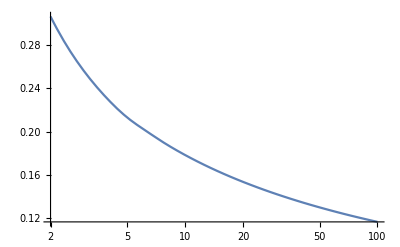

```mathematica
LogLinearPlot[pdfAlphaS[1,q],{q,2,100}]
```

## Example: Plotting Single Functions

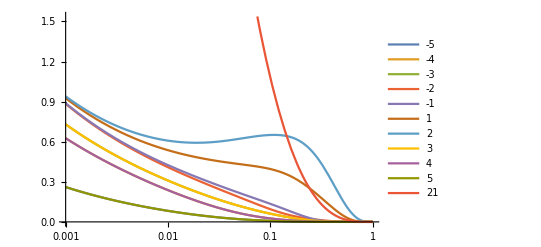

```mathematica
Clear[x];
q0=10. ;
LogLinearPlot[ x pdf[1,flavors,x,q0] //Evaluate,{x,10^-3,1},PlotLegends->flavors]
```

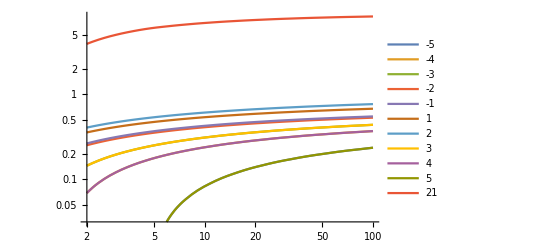

```mathematica
Clear[q];
x0=0.01 ;
LogLogPlot[ x0 pdf[1,flavors,x0,q] //Evaluate,{q,2,100},PlotLegends->flavors]
```

## Example: 3D Plots

```mathematica
xlist=Table[10.^i,{i,-4,0,1/4}];
qlist=Table[1.3 * 10.^i,{i,0,2,1/4}];
data=Table[{x= xlist[[i]],q=qlist[[j]], x pdf[1,1,x,q]},{i,1,Length[xlist]},{j,1,Length[qlist]}] ;
```

```mathematica
ListPlot3D[data //Flatten[#,1]&,ScalingFunctions->{"Log","Log","Log"}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[data,ScalingFunctions->{"Log","Log","Log"},
Filling->Bottom]
```

-Graphics3D-

```mathematica
Get[pdfParseLHA.m]
iSet1=pdfParseLHA[LHA file.info,LHA file.dat]
pdfFunction[iSet1,iParton,x,Q]
```

Get::stream: pdfParseLHA.m is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

pdfParseLHA[LHA file.info,LHA file.dat]

pdfFunction[pdfParseLHA[LHA file.info,LHA file.dat],iParton,x,Q]